```mathematica
WM=ResourceFunction["WolframModel"];
```

```mathematica
rule= {{{1,2},{1,3}}->{{1,4},{4,5},{5,2},{3,5}}};
steps=10;
```

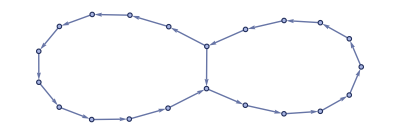

```mathematica
WM[rule,Automatic,10,"FinalStatePlot"]
```

## Graph Mutations

Remove random vertex (and edges incident to it)

Add random vertex (and some number of edges to it)

Add random edge between existing vertices

Remove random edge (clear disconnected vertices?)

Modify random edge (change one vertex to a different one)

```mathematica
WolframRuleToEdgeRules[rule_List]:=Apply[DirectedEdge,rule,{3}]
EdgeRulesWolframToRule[edges_List]:=Apply[List,edges,{3}]
```

```mathematica
edges=RuleToEdges[rule]
```

{{1->2,1->3}→{1->4,4->5,5->2,3->5}}

```mathematica
EdgesToRule[edges]
```

{{{1,2},{1,3}}→{{1,4},{4,5},{5,2},{3,5}}}

```mathematica
rule
```

{{{1,2},{1,3}}→{{1,4},{4,5},{5,2},{3,5}}}

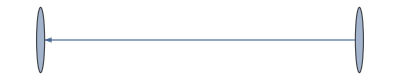

```mathematica
Graph[First@edges]
```

```mathematica
Graph[Last@edges]
```

-Graphics-

```mathematica
rule
```

{{{1,2},{1,3}}→{{1,4},{4,5},{5,2},{3,5}}}

```mathematica
edgeRules=Apply[DirectedEdge,rule,{3}]
```

{{1->2,1->3}→{1->4,4->5,5->2,3->5}}

```mathematica
FullForm[edgeRules]
```

List[Rule[List[DirectedEdge[1,2],DirectedEdge[1,3]],List[DirectedEdge[1,4],DirectedEdge[4,5],DirectedEdge[5,2],DirectedEdge[3,5]]]]

```mathematica
RandomChoice
```

```mathematica
Position[rule,_,{4},Heads->False]
```

{{1,1,1,1},{1,1,1,2},{1,1,2,1},{1,1,2,2},{1,2,1,1},{1,2,1,2},{1,2,2,1},{1,2,2,2},{1,2,3,1},{1,2,3,2},{1,2,4,1},{1,2,4,2}}

```mathematica
wm = ResourceFunction["WolframModel"];
plot = ResourceFunction["WolframModelPlot"];
randomRule = ResourceFunction["RandomWolframModel"];
```

```mathematica
randomSignature[maxRelations_, maxElements_, maxPieces_] := 
	Rule @@ Table[
		Table[
			{RandomInteger[{1, maxRelations}], RandomInteger[{1, maxElements}]},
			RandomInteger[{1, maxPieces}]
		], 
		2
	]
```

```mathematica
steps=10;
maxValue = 3;
maxVertices=3;
```

```mathematica
signature={{2,2}}->{{4,2}};
rule = {{{1,2},{1,3}}->{{1,4},{4,5},{5,2},{3,5}}};
```

```mathematica
wm[rule, Automatic, steps, "FinalStatePlot"]
```

-Graphics-

```mathematica
replaceRandomElement[rule_] :=
	Module[{pos, elem, maxElem, choices},
		pos = RandomChoice[Position[rule, _, {4}, Heads -> False]];
		elem = Extract[rule, pos];
		maxElem = maxElement[rule];
		choices = If[maxElem > 1, Delete[Range[1, maxElem], elem], {1}];
		ReplacePart[rule, pos->RandomChoice[choices]]
	]
```

```mathematica
rule
```

{{{1,2},{1,3}}→{{1,4},{4,5},{5,2},{3,5}}}

```mathematica
maxElement[rule_] := Max[Flatten[List @@@ rule]]
```

```mathematica
replaceRandomElement[rule]
```

{{{1,2},{1,3}}→{{1,4},{4,5},{5,2},{3,1}}}

```mathematica
rule
```

{{{1,2},{1,3}}→{{1,4},{4,5},{5,2},{3,5}}}

```mathematica
addRandomEdge[rule_]:=
	Module[{pos, edges,newEdge, maxElem, choices},
		pos = RandomChoice[Position[rule, _, {2}, Heads -> False]];
		edges = Extract[rule, pos];
		maxElem = maxElement[rule];
		newEdge = Table[RandomInteger[{1, maxElem}], 2];
		ReplacePart[rule, pos -> Append[edges, newEdge]]
	]
```

```mathematica
addRandomEdge[rule]
```

{{{1,2},{1,3},{2,5}}→{{1,4},{4,5},{5,2},{3,5}}}

```mathematica
addRandomElement[rule_]:=
	Module[{pos, edge, maxElem, choices},
			pos = RandomChoice[Position[rule, _, {3}, Heads -> False]];
			edge = Extract[rule, pos];
			maxElem = maxElement[rule];
			ReplacePart[rule, pos -> Append[edge, RandomInteger[{1, maxElem+1}]]]
		]
```

```mathematica
addRandomElement[rule]
```

{{{1,2},{1,3}}→{{1,4},{4,5,4},{5,2},{3,5}}}

```mathematica
removeRandomElement[rule_]:=
	Module[{pos, edge, newEdge, choices},
			pos = RandomChoice[Position[rule, _, {3}, Heads -> False]];
			edge = Extract[rule, pos];
			newEdge = Delete[edge, RandomInteger[{1, Length[edge]}]] /. {} :> Nothing;
			ReplacePart[rule, pos -> newEdge]
		]
```

```mathematica
r=removeRandomElement[rule]
```

{{{1,2},{1,3}}→{{1,4},{4},{5,2},{3,5}}}

```mathematica
NestList[removeRandomElement, rule, 10]//Column
```

```mathematica
{{{{{1,2},{1,3}}->{{1,4},{4,5},{5,2},{3,5}}}}, {{{{1},{1,3}}->{{1,4},{4,5},{5,2},{3,5}}}}, {{{{1},{3}}->{{1,4},{4,5},{5,2},{3,5}}}}, {{{{1},{3}}->{{1,4},{4,5},{5,2},{5}}}}, {{{{1},{3}}->{{1,4},{4,5},{5,2}}}}, {{{{1}}->{{1,4},{4,5},{5,2}}}}, {{{{1}}->{{1,4},{4,5},{2}}}}, {{{}->{{1,4},{4,5},{2}}}}, {{{}->{{1,4},{4,5}}}}, {{{}->{{4},{4,5}}}}, {{{}->{{4},{5}}}}}
```